```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datamar=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/marginals.dat"];
datamarx=Table[{datamar[[i,1]],datamar[[i,2]]},{i,1,Length[datamar]}];
datamarp=Table[{datamar[[i,1]],datamar[[i,3]]},{i,1,Length[datamar]}];
```

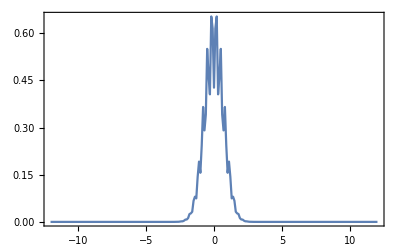

```mathematica
ListPlot[datamarp,Joined->True,PlotRange->All,Frame->True]
```

```mathematica
dx=0.1;
ratioFromData[mar_List]:=Module[{f,idx,x0,solMax,a,fa,f2a,ratio},
f=Interpolation[mar,Method->"Spline"];
idx=Ordering[mar[[All,2]],-1][[1]];
x0=mar[[idx,1]];
solMax=FindMaximum[{f[x],x0-dx<=x<=x0+dx},{x,x0}];
a=x/. solMax[[2]];
fa=f[a];
f2a=f''[a];
ratio=fa/Abs[f2a];
<|"a"->a,"f(a)"->fa,"f''(a)"->f2a,"ratio"->ratio,"f"->f|>];
```

```mathematica
ratioFromData[datamarp]
```

<|a→0.161911,f(a)→0.685414,f''(a)→-41.7256,ratio→0.0164267,f→InterpolatingFunction[…]|>